```mathematica
ass=Assumptions->{kx,ky,kz,k,θ,χ,ϕ,θp,ϕp,kp,cq,vf,B,μ,chi,fac} ∈ Reals && k>0 && kp>0 && 0<=θ<=π && 0<=θp<=π && βtra>0 && βter>0 && cq>=0 && vf>0 && B>0;
```

## phys quantities

```mathematica
rep={kx->k Sin[θ] Cos[ϕ],ky->k Sin[θ] Sin[ϕ],kz->k Cos[θ]};
ass=Assumptions->{kx,ky,kz,k,θ,ϕ,θp,ϕp,kp,vinter,vinter} ∈ Reals && k>0 && kp>0 && 0<=θ<=π && 0<=θp<=π && vintra>0 && vinter>0;
en0=vf^2(kx^2+ky^2+kz^2);
Print["band vel."];
v0=FullSimplify[Grad[en0,{kx,ky,kz}]/.rep,ass]
Print["v0.k"];
v0dotk=FullSimplify[v0.{kx,ky,kz}/.rep,Assumptions->k ∈ Reals && k>0]
Print["BC vector"];
Ω=(-2 kz)/((kx^2+ky^2+kz^2)^2){ kx ,ky ,kz};FullSimplify[Ω/.rep,ass]
ommvec=(-2e vf^2 kz)/(kx^2+ky^2+kz^2){  kx,ky,kz};
Print["OMM energy"];
enom=-ommvec.{0,0,Bz};
FullSimplify[enom/.rep,ass]
Print["OMM correc. to band vel."];
vm=FullSimplify[Grad[enom,{kx,ky,kz}],ass]
FullSimplify[vm/.rep,ass]
Print["vm.k"];
vmdotk=FullSimplify[vm.{kx,ky,kz}/.rep,Assumptions->k ∈ Reals && k>0]
Print["v.Ω"];
FullSimplify[(v0+vm).Ω/.rep,Assumptions->k ∈ Reals && k>0]
```

band vel.

{2 k vf^2 Cos[ϕ] Sin[θ],2 k vf^2 Sin[θ] Sin[ϕ],2 k vf^2 Cos[θ]}

v0.k

2 k^2 vf^2

BC vector

{-(Cos[ϕ] Sin[2 θ])/k^2,-(Sin[2 θ] Sin[ϕ])/k^2,-(2 Cos[θ]^2)/k^2}

OMM energy

2 Bz e vf^2 Cos[θ]^2

OMM correc. to band vel.

{-(4 Bz e kx kz^2 vf^2)/((kx^2+ky^2+kz^2)^2),-(4 Bz e ky kz^2 vf^2)/((kx^2+ky^2+kz^2)^2),(4 Bz e (kx^2+ky^2) kz vf^2)/((kx^2+ky^2+kz^2)^2)}

{-(4 Bz e vf^2 Cos[θ]^2 Cos[ϕ] Sin[θ])/k,-(4 Bz e vf^2 Cos[θ]^2 Sin[θ] Sin[ϕ])/k,(4 Bz e vf^2 Cos[θ] Sin[θ]^2)/k}

vm.k

0

v.Ω

-(4 vf^2 Cos[θ])/k

## sigma

```mathematica
Solve[vf^2 kf^2+2 Bz e vf^2 Cos[θ]^2==μ,kf]
```

{{kf→-(√(μ-2 Bz e vf^2 Cos[θ]^2))/vf},{kf→(√(μ-2 Bz e vf^2 Cos[θ]^2))/vf}}

```mathematica
Clear[sig];
sig[B_,βintra_,βinter_]:=Block[{e=1,μ=0.1,vf=0.005,BCvec,v0vec,vmvec,matr,rhs1,rhs2,θ,τ,kf,f,vdotk,α,conteq,λ1,λ2,a1,a2,cost,θp,ϕ,Dphase,h,zero,c2t,c2tc2t,hzero,hc2t,colvec,mat,sol,sol1,Λ1,Λ2,s1,s2,int1,int2},
kf[θ_]= (√(μ-2 B e vf^2 Cos[θ]^2))/vf ;
BCvec[θ_]=-1/kf[θ]^2{ Sin[2 θ]Cos[ϕ],Sin[2 θ] Sin[ϕ],2 Cos[θ]^2};
Dphase[θ_]=1 +e (BCvec[θ])[[3]] B;
v0vec[θ_]=2kf[θ] vf^2{  Cos[ϕ] Sin[θ], Sin[θ] Sin[ϕ], Cos[θ]};
vmvec[θ_]=(2 Sin[2θ]e B vf^2)/kf[θ]{-Cos[θ] Cos[ϕ] ,- Cos[θ] Sin[ϕ], Sin[θ]};
vdotk[θ_]=2 kf[θ]^2 vf^2;
h[θ_]=1/Dphase[θ]((v0vec[θ]+vmvec[θ])[[3]]-e B  (4 vf^2 Cos[θ])/kf[θ]);
(******** 1/2 (1+Cos[2 θ] Cos[2 θp]) ***********)
τ[θ_]=(βintra/2 NIntegrate [(Sin[θp] (kf[θp])^3)/Abs[vdotk[θp]] Dphase[θp],{θp,0,π}]+
βintra/2  Cos[2θ] NIntegrate [(Sin[θp] (kf[θp])^3)/Abs[vdotk[θp]] Dphase[θp]Cos[2θp],{θp,0,π}])^-1;

f[θ_]=(Sin[θ] (kf[θ])^3)/Abs[vdotk[θ]] Dphase[θ] τ[θ];
zero=Quiet[NIntegrate [f[θp],{θp,0,π}]];
c2t=Quiet[NIntegrate [f[θp] Cos[2θp],{θp,0,π}]];
c2tc2t=Quiet[NIntegrate [f[θp] Cos[2θp]^2,{θp,0,π}]];
hzero=Quiet[NIntegrate [f[θp] h[θp],{θp,0,π}]];
hc2t=Quiet[NIntegrate [f[θp]h[θp]Cos[2θp],{θp,0,π}]];
colvec=({{1/2 hzero βintra}, {1/2 hc2t βintra}});
matr=({{1-(zero βintra)/2, -(c2t βintra)/2}, {-(c2t βintra)/2, 1-(c2tc2t βintra)/2}});
mat=matr.{λ1,a1};
sol1=LinearSolve[matr,-colvec]//Chop;
conteq=(λ1 zero-hzero+a1 c2t)+(λ2 zero-hzero+a2 c2t);

sol=Flatten[Solve[{mat[[1]]+colvec[[1]]==0,mat[[2]]+colvec[[2]]==0},{λ1,a1}],1]//Chop;

(*Λ1[θ_]=τ[θ](λ1-h[θ]+a1 Cos[2θ])/.sol;
Λ2[θ_]=τ[θ](λ2-h[θ]+a2 Cos[2θ])/.sol;

 -Graphics- *)
(*int1[θ_]=-(Sin[θ] (kf[θ])^3)/Abs[vdotk[θ]]e Dphase[θ] h[θ]Λ1[θ];
int2[θ_]=-(Sin[θ] (kf[θ])^3)/Abs[vdotk[θ]]e Dphase[θ] h[θ]Λ1[θ];

s1=NIntegrate[int1[θ],{θ,0,π}];
s2=NIntegrate[int2[θ],{θ,0,π}];*)
{B,sol1,sol,MatrixForm[{λ1,a1}/.sol],MatrixRank[matr]}
];
sig[10,1,0.5]
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{0.0656881,0.196276},{0.196276,0.586472}} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{0.196276,0.0656881,-3.36696×10^-20},{0.586472,0.196276,5.75982×10^-20}} may contain significant numerical errors.

{10,{-1.18581×10^-7,3.96859×10^-8},{λ1→-1.18579×10^-7,a1→3.96852×10^-8},(-1.18579×10^-7
3.96852×10^-8),2}

## Results

{{-10,8.37708×10^-7},{-9,8.37271×10^-7},{-8,8.36833×10^-7},{-7,8.36396×10^-7},{-6,8.35958×10^-7},{-5,8.35521×10^-7},{-4,8.35083×10^-7},{-3,8.34646×10^-7},{-2,8.34208×10^-7},{-1,8.33771×10^-7},{0,8.33333×10^-7},{1,8.32896×10^-7},{2,8.32458×10^-7},{3,8.32021×10^-7},{4,8.31583×10^-7},{5,8.31146×10^-7},{6,8.30708×10^-7},{7,8.30271×10^-7},{8,8.29833×10^-7},{9,8.29396×10^-7},{10,8.28958×10^-7}}

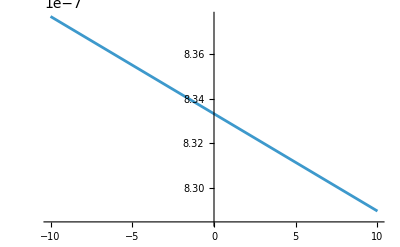

```mathematica
vintra=3;vinter=vintra/2;
dat1=Table[Quiet[sig[B,vintra,vinter]],{B,-10,10,1}];
list=dat1;
len=Length[list];
scale=1(*list[[1,2]]*);
dat=Table[{list[[i,1]],list[[i,2]]scale},{i,1,len}]
ListLinePlot[{dat}]
```

{{-10,5.58333×10^-7},{-9,5.58056×10^-7},{-8,5.57778×10^-7},{-7,5.575×10^-7},{-6,5.57222×10^-7},{-5,5.56944×10^-7},{-4,5.56667×10^-7},{-3,5.56389×10^-7},{-2,5.56111×10^-7},{-1,5.55833×10^-7},{0,5.55556×10^-7},{1,5.55278×10^-7},{2,5.55×10^-7},{3,5.54722×10^-7},{4,5.54444×10^-7},{5,5.54167×10^-7},{6,5.53889×10^-7},{7,5.53611×10^-7},{8,5.53333×10^-7},{9,5.53056×10^-7},{10,5.52778×10^-7}}

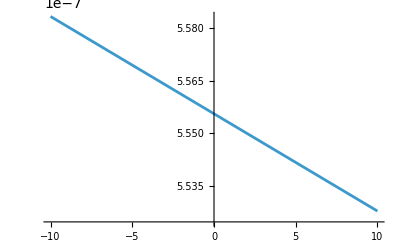

```mathematica
vintra=3;vinter=vintra;
dat1=Table[Quiet[sig[B,vintra,vinter]],{B,-10,10,1}];
list=dat1;
len=Length[list];
scale=1(*list[[1,2]]*);
dat=Table[{list[[i,1]],list[[i,2]]scale},{i,1,len}]
ListLinePlot[{dat}]
```

{{-10,3.34933×10^-7},{-9,3.34773×10^-7},{-8,3.34613×10^-7},{-7,3.34453×10^-7},{-6,3.34293×10^-7},{-5,3.34133×10^-7},{-4,3.33973×10^-7},{-3,3.33813×10^-7},{-2,3.33653×10^-7},{-1,3.33493×10^-7},{0,3.33333×10^-7},{1,3.33173×10^-7},{2,3.33013×10^-7},{3,3.32853×10^-7},{4,3.32693×10^-7},{5,3.32533×10^-7},{6,3.32373×10^-7},{7,3.32213×10^-7},{8,3.32053×10^-7},{9,3.31893×10^-7},{10,3.31733×10^-7}}

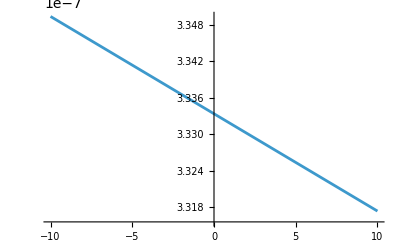

```mathematica
vintra=3;vinter=2vintra;
dat1=Table[Quiet[sig[B,vintra,vinter]],{B,-10,10,1}];
list=dat1;
len=Length[list];
scale=1(*list[[1,2]]*);
dat=Table[{list[[i,1]],list[[i,2]]scale},{i,1,len}]
ListLinePlot[{dat}]
```